# Home Page Graphics

```mathematica
SetDirectory["/Users/Masaya/Documents/ChatGPT/Home Page/public/images/publications"];
```

## CHPT

```mathematica
Module[{a=.25,c=1,mu,ellm,m,n,z,r,f,nu,ft},
mu=2/(a+c);
ellm=(c^2-a^2)/c^2;
m=(c^2-a^2)/2;
n=(c^2+a^2)/2;
z[u_]:=a EllipticF[mu u/2-Pi/4,ellm]+c EllipticE[mu u/2-Pi/4,ellm];
r[u_]:=Sqrt[m Sin[mu u]+n];
f[u_,v_]:={z[u],r[u] Cos[v],r[u] Sin[v]};
nu[u_,v_]:=Normalize[{-r'[u],z'[u] Cos[v],z'[u] Sin[v]}];
ft[u_,v_,t_]:=f[u,v]+t nu[u,v];

Show[
ParametricPlot3D[ft[u,v,2],{u,-4.75,6.75},{v,0,2 Pi},
PlotPoints->{100,100},
PlotStyle->Directive[blue,Opacity[.3]],
MeshFunctions->{#1&},
Mesh->10
],
ParametricPlot3D[f[u,v],{u,-4.75,6.75},{v,0,2 Pi},
PlotPoints->{50,50},
PlotStyle->GrayLevel[.7,.7],
MeshFunctions->{#1&}
],
PlotRange->All,
Boxed->False,
Axes->False,
Lighting->"Neutral",
Background->None,
ImageSize->{600,600},
ImagePadding->0,
PlotRangePadding->Scaled[.02],
ViewAngle->.28598564241059005,
ViewCenter->{{.5,.5,.5},{.48818359375,.5368944846827949}},
ViewPoint->{-.9217395220986987,-1.3044140050215869,-2.982585515438712},
ViewVertical->{-.3507233135430239,.5026162826639182,-.7901708864154044}
]
]
```

-Graphics3D-

```mathematica
Module[{a=.25,c=1,mu,ellm,m,n,z,r,f,nu,ft},
mu=2/(a+c);
ellm=(c^2-a^2)/c^2;
m=(c^2-a^2)/2;
n=(c^2+a^2)/2;
z[u_]:=a EllipticF[mu u/2-Pi/4,ellm]+c EllipticE[mu u/2-Pi/4,ellm];
r[u_]:=Sqrt[m Sin[mu u]+n];
f[u_,v_]:={z[u],r[u] Cos[v],r[u] Sin[v]};
nu[u_,v_]:=Normalize[{-r'[u],z'[u] Cos[v],z'[u] Sin[v]}];
ft[u_,v_,t_]:=f[u,v]+t nu[u,v];

Export["chpt2025.png",
Show[
ParametricPlot3D[ft[u,v,2],{u,-4.75,6.75},{v,0,2 Pi},
PlotPoints->{100,100},
PlotStyle->Directive[blue,Opacity[.3]],
MeshFunctions->{#1&},
Mesh->10
],
ParametricPlot3D[f[u,v],{u,-4.75,6.75},{v,0,2 Pi},
PlotPoints->{50,50},
PlotStyle->GrayLevel[.7,.7],
MeshFunctions->{#1&}
],
PlotRange->All,
Boxed->False,
Axes->False,
Lighting->"Neutral",
Background->None,
ImageSize->{600,600},
ImagePadding->0,
PlotRangePadding->Scaled[.02],
ViewAngle->.28598564241059005,
ViewCenter->{{.5,.5,.5},{.48818359375,.5368944846827949}},
ViewPoint->{-.9217395220986987,-1.3044140050215869,-2.982585515438712},
ViewVertical->{-.3507233135430239,.5026162826639182,-.7901708864154044}
],
Background->None,
ImageResolution->144
]
];
```

## mathsci

```mathematica
Module[{c=1,k=2,g,ω,f},
g[z_]=-ⅇ^z(c(1+k)+(1-k)ⅇ^(k*z))/(c(1-k)+(1+k)ⅇ^(k*z));
ω[z_]=1/D[g[z],z]//Simplify;
f[z_]=Re@Integrate[{1+g[z]^2,ⅈ(1-g[z]^2),-2g[z]}ω[z],z]+{0,0,8/3};
ParametricPlot3D[f[u+ⅈ*v],{u,-2.5,2.5},{v,-π,π},
(*PlotPoints->5*10^2,*)
PlotPoints->100,
MeshFunctions->{#4&},
Mesh->20,
PlotRange->4,
Boxed->False,
Axes->False,
Lighting->"Neutral",
Background->None,
ImageSize->{600,600},
ImagePadding->0,
PlotRangePadding->Scaled[.02],
PlotStyle->Directive[red,Opacity[.8]],
ViewAngle->0.3546312712899884,ViewCenter->{{0.5,0.5,0.5},{0.5060730957960334,0.5162458559005623}},ViewPoint->{2.5851908949541897,-1.8840975844345025,1.0823217308056008},ViewVertical->{0.22075552254266387,-0.13646707358703739,0.9657348171695508}
]
]
```

-Graphics3D-

```mathematica
Module[{c=1,k=2,g,ω,f},
g[z_]=-ⅇ^z(c(1+k)+(1-k)ⅇ^(k*z))/(c(1-k)+(1+k)ⅇ^(k*z));
ω[z_]=1/D[g[z],z]//Simplify;
f[z_]=Re@Integrate[{1+g[z]^2,ⅈ(1-g[z]^2),-2g[z]}ω[z],z]+{0,0,8/3};

Export["mathsci.png",
ParametricPlot3D[f[u+ⅈ*v],{u,-2.5,2.5},{v,-π,π},
(*PlotPoints->5*10^2,*)
PlotPoints->100,
MeshFunctions->{#4&},
Mesh->20,
PlotRange->4,
Boxed->False,
Axes->False,
Lighting->"Neutral",
Background->None,
ImageSize->{600,600},
ImagePadding->0,
PlotRangePadding->Scaled[.02],
PlotStyle->Directive[red,Opacity[.8]],
ViewAngle->0.3546312712899884,ViewCenter->{{0.5,0.5,0.5},{0.5060730957960334,0.5162458559005623}},ViewPoint->{2.5851908949541897,-1.8840975844345025,1.0823217308056008},ViewVertical->{0.22075552254266387,-0.13646707358703739,0.9657348171695508}
],
Background->None,
ImageResolution->144
]
];
```

## acho2025

```mathematica
Module[{g,ee,l,ϵ,eps,reg,η,hη,h2η,fp,epsP,epsS,p,q},
g=N[WeierstrassInvariants[{1/2,ⅈ/2}]];
ee=N[WeierstrassP[1/2,g]];
l=Re[WeierstrassZeta[(1+ⅈ)/2,g]];
ϵ=0.01;
eps=0.075;
epsP=0.01;
epsS=0.010;
reg=ImplicitRegion[Abs[u-1/2]+Abs[v]<=1/2+0.01&&u^2+v^2>=epsP^2&&(u-1)^2+v^2>=epsP^2&&(u-1/2)^2+v^2>=epsS^2,{u,v}];

η[z_]=-WeierstrassZeta[z,g]+WeierstrassZeta[(1+ⅈ)/2,g];
hη[z_]=(√(2π))/4(Log[Abs[(WeierstrassP[z,g]-ee)/(WeierstrassP[z,g]+ee)]]-ⅈ*π);
h2η[z_]=-(π*z+π/(2ee)(WeierstrassZeta[z-1/2,g]-WeierstrassZeta[z-ⅈ/2,g])-(1+ⅈ)/2 π+(1+ⅈ)/(4ee)π^2);
fp[z_]={η[z],-ⅈ*η[z],hη[z]};

p[1]=First@ParametricPlot3D[Re@N@fp[u+ⅈ*v],{u,v}∈reg,
PlotPoints->200,
MaxRecursion->6,
MeshStyle->None,
MeshFunctions->{#3&},
Mesh->14,
MeshShading->{{green,Opacity[0.7]},{White,Opacity[1.0]}},
Lighting->"Neutral",
PlotRange->{{-10,10},{-10,10},{-5,5}},
Boxed->True,
Axes->True,
Ticks->True,
ViewPoint->{0, -2, 2}
];

p[2]={p[1],GeometricTransformation[p[1],TranslationTransform[{0,2l,0}]]};
p[3]={p[2],GeometricTransformation[p[1],TranslationTransform[{0,-2l,0}]],GeometricTransformation[p[1],TranslationTransform[{0,4l,0}]]};
p[4]={p[3],GeometricTransformation[p[3],TranslationTransform[{2l,0,0}]]};
q[1]=GeometricTransformation[p[1],RotationTransform[π/2,{0,0,1}]@*ReflectionTransform[{0,0,1}]];
q[2]={q[1],GeometricTransformation[q[1],TranslationTransform[{0,2l,0}]]};
q[3]={q[2],GeometricTransformation[q[1],TranslationTransform[{0,-2l,0}]]};
q[4]={q[3],GeometricTransformation[q[3],TranslationTransform[{2l,0,0}]]};

Graphics3D[
{
p[4],
q[4]
},
Lighting->"Neutral",
PlotRange->{{-6,8},{-8,8},{-5,5}},
Boxed->False,
Axes->False,
Ticks->False,
ViewPoint->{3,-1,-1},
ViewVertical->{0,0,-1},
ViewAngle->0.3829519167479297,ViewCenter->{{0.5,0.5,0.5},{0.5369140625,0.5331510416666667}},
ImageSize->{600,600}
]
]
```

-Graphics3D-

```mathematica
Module[{g,ee,l,ϵ,eps,reg,η,hη,h2η,fp,epsP,epsS,p,q},
g=N[WeierstrassInvariants[{1/2,ⅈ/2}]];
ee=N[WeierstrassP[1/2,g]];
l=Re[WeierstrassZeta[(1+ⅈ)/2,g]];
ϵ=0.01;
eps=0.075;
epsP=0.01;
epsS=0.010;
reg=ImplicitRegion[Abs[u-1/2]+Abs[v]<=1/2+0.01&&u^2+v^2>=epsP^2&&(u-1)^2+v^2>=epsP^2&&(u-1/2)^2+v^2>=epsS^2,{u,v}];

η[z_]=-WeierstrassZeta[z,g]+WeierstrassZeta[(1+ⅈ)/2,g];
hη[z_]=(√(2π))/4(Log[Abs[(WeierstrassP[z,g]-ee)/(WeierstrassP[z,g]+ee)]]-ⅈ*π);
h2η[z_]=-(π*z+π/(2ee)(WeierstrassZeta[z-1/2,g]-WeierstrassZeta[z-ⅈ/2,g])-(1+ⅈ)/2 π+(1+ⅈ)/(4ee)π^2);
fp[z_]={η[z],-ⅈ*η[z],hη[z]};

p[1]=First@ParametricPlot3D[Re@N@fp[u+ⅈ*v],{u,v}∈reg,
PlotPoints->200,
MaxRecursion->6,
MeshStyle->None,
MeshFunctions->{#3&},
Mesh->14,
MeshShading->{{green,Opacity[0.7]},{White,Opacity[1.0]}},
Lighting->"Neutral",
PlotRange->{{-10,10},{-10,10},{-5,5}},
Boxed->True,
Axes->True,
Ticks->True,
ViewPoint->{0, -2, 2}
];

p[2]={p[1],GeometricTransformation[p[1],TranslationTransform[{0,2l,0}]]};
p[3]={p[2],GeometricTransformation[p[1],TranslationTransform[{0,-2l,0}]],GeometricTransformation[p[1],TranslationTransform[{0,4l,0}]]};
p[4]={p[3],GeometricTransformation[p[3],TranslationTransform[{2l,0,0}]]};
q[1]=GeometricTransformation[p[1],RotationTransform[π/2,{0,0,1}]@*ReflectionTransform[{0,0,1}]];
q[2]={q[1],GeometricTransformation[q[1],TranslationTransform[{0,2l,0}]]};
q[3]={q[2],GeometricTransformation[q[1],TranslationTransform[{0,-2l,0}]]};
q[4]={q[3],GeometricTransformation[q[3],TranslationTransform[{2l,0,0}]]};

Export["acho2025.png",
Graphics3D[
{
p[4],
q[4]
},
Lighting->"Neutral",
PlotRange->{{-6,8},{-8,8},{-5,5}},
Boxed->False,
Axes->False,
Ticks->False,
ViewPoint->{3,-1,-1},
ViewVertical->{0,0,-1},
ViewAngle->0.3829519167479297,ViewCenter->{{0.5,0.5,0.5},{0.5369140625,0.5331510416666667}},
ImageSize->{600,600}
],
Background->None,
ImageResolution->144
]
];
```

## ch2026

```mathematica
Module[{h,η,f,uu=1,vv=3/2 π},
h[z_]=Coth[z];
η[z_]=Sinh[z]^2;
f[z_]=Re@Integrate[{1,ⅈ,h[z]}η[z],z];
ParametricPlot3D[f[u+ⅈ*v],{u,-uu,uu},{v,-vv,vv},
PlotRange->All,
PlotPoints->500,
MeshFunctions->{#4&},
Mesh->13,
PlotStyle->Directive[green,Opacity[0.8]],
ViewAngle->0.31990987866626097,ViewCenter->{{0.5,0.5,0.5},{0.5086298372098104,0.530187553108111}},ViewPoint->{-2.859321862164624,1.5874862194755768,1.0400798005550183},ViewVertical->{0.02357652574597465,0.015627604631329946,0.9995998826566739},
ImageSize->{600,600}
]
]
```

-Graphics3D-

```mathematica
Module[{h,η,f,uu=1,vv=3/2 π},
h[z_]=Coth[z];
η[z_]=Sinh[z]^2;
f[z_]=Re@Integrate[{1,ⅈ,h[z]}η[z],z];
Export["ch2026.png",
ParametricPlot3D[f[u+ⅈ*v],{u,-uu,uu},{v,-vv,vv},
PlotRange->All,
PlotPoints->500,
MeshFunctions->{#4&},
Mesh->13,
PlotStyle->Directive[green,Opacity[0.8]],
ViewAngle->0.31990987866626097,ViewCenter->{{0.5,0.5,0.5},{0.5086298372098104,0.530187553108111}},ViewPoint->{-2.859321862164624,1.5874862194755768,1.0400798005550183},ViewVertical->{0.02357652574597465,0.015627604631329946,0.9995998826566739},
ImageSize->{600,600}
],
Background->None,
ImageResolution->144
]
];
```

## phd

```mathematica
Module[{h2η,η,hη,f,p,k=3},
h2η[z_]:=-(z^(-1+k) (k+(-1+k) (-1+z^k) LerchPhi[z^k,1,1-1/k]))/(k^2 (-1+z^k));
η[z_]:=(z (1/(1-z^k)+((-1+k) LerchPhi[z^k,1,1/k])/k))/k;
hη[z_]:=1/(k-k z^k);
f[z_]:={η[z],-ⅈ*η[z],hη[z]};

p[1]=First@ParametricPlot3D[
Re[f[(1+2/(ⅈ Exp[x+ⅈ y]-1))^(2/k)]]
,{x,0,2}
,{y,-π/2,π/2}
,PlotPoints->10*{8,16}
,Mesh->6
,MeshStyle->(*GrayLevel[.5]*)None
,MeshFunctions->{#4&}
,MeshShading->{{green,Opacity[.75]},GrayLevel[.9]}
];

p[2]={p[1],GeometricTransformation[p[1],ReflectionTransform[{0,1,0}]]};

Graphics3D[

Table[GeometricTransformation[p[2],RotationTransform[n/k 2π,{0,0,1}]],{n,0,k-1}]

,ImageSize->{600,600}
,Boxed->False
,Lighting->"Neutral"

,PlotRange->{{-5,5},{-5,5},{-5,5}},
ViewAngle->0.616389041611263,
ViewCenter->{{0.5,0.5,0.5},{0.5032161458333333,0.455546875}}
,ViewVertical->{0,0,1}
,With[{r=5,θ=π/3,ϕ=π/180 40},
ViewVector->{
r{Cos[θ]Cos[ϕ],Sin[θ]Cos[ϕ],Sin[ϕ]},
{0,0,0}
}
]
]
]
```

-Graphics3D-

```mathematica
Module[{h2η,η,hη,f,p,k=3},
h2η[z_]:=-(z^(-1+k) (k+(-1+k) (-1+z^k) LerchPhi[z^k,1,1-1/k]))/(k^2 (-1+z^k));
η[z_]:=(z (1/(1-z^k)+((-1+k) LerchPhi[z^k,1,1/k])/k))/k;
hη[z_]:=1/(k-k z^k);
f[z_]:={η[z],-ⅈ*η[z],hη[z]};

p[1]=First@ParametricPlot3D[
Re[f[(1+2/(ⅈ Exp[x+ⅈ y]-1))^(2/k)]]
,{x,0,2}
,{y,-π/2,π/2}
,PlotPoints->10*{8,16}
,Mesh->6
,MeshStyle->(*GrayLevel[.5]*)None
,MeshFunctions->{#4&}
,MeshShading->{{green,Opacity[.75]},GrayLevel[.9]}
];

p[2]={p[1],GeometricTransformation[p[1],ReflectionTransform[{0,1,0}]]};

Export["phd.png",
Graphics3D[

Table[GeometricTransformation[p[2],RotationTransform[n/k 2π,{0,0,1}]],{n,0,k-1}]

,ImageSize->{600,600}
,Boxed->False
,Lighting->"Neutral"

,PlotRange->{{-5,5},{-5,5},{-5,5}},
ViewAngle->0.616389041611263,
ViewCenter->{{0.5,0.5,0.5},{0.5032161458333333,0.455546875}}
,ViewVertical->{0,0,1}
,With[{r=5,θ=π/3,ϕ=π/180 40},
ViewVector->{
r{Cos[θ]Cos[ϕ],Sin[θ]Cos[ϕ],Sin[ϕ]},
{0,0,0}
}
]
],
Background->None,
ImageResolution->144
]
];
```

## ch2027

```mathematica
Module[{M,N,Y,mS,mE,nS,nE},
{M,N}={6,2};
{mS,mE}={-4,4};
{nS,nE}={-5,5};
Y[m_,n_]={1/(2M)((M+N)(m/N)^2+(M-N)(n/N)^2),m/N,n/N};

Graphics3D[{
EdgeForm[{green,Thickness[0.005]}],
FaceForm[{White}],
Opacity[0.3],
Lighting->"Accent",
Polygon[
Flatten[
Table[
Table[
{{Y[m,n],Y[m+1,n],Y[m+1,n+1],Y[m,n+1]}}
,{m,mS,mE-1}]
,{n,nS,nE-1}]
,2]
]
},
Boxed->False,
ViewCenter->{{0.5,0.5,0.5},{0.5072619047551542,0.40352040825295354}},ViewPoint->{0.9679528102582141,-2.6884974853053145,1.8124703111003586},ViewVertical->{0.9608127331811807,-0.24712328585999074,0.12557457283491208},
ImageSize->{600,600}
]
]
```

-Graphics3D-

```mathematica
Module[{M,N,Y,mS,mE,nS,nE},
{M,N}={6,2};
{mS,mE}={-4,4};
{nS,nE}={-5,5};
Y[m_,n_]={1/(2M)((M+N)(m/N)^2+(M-N)(n/N)^2),m/N,n/N};

Export["ch2027.png",
Graphics3D[{
EdgeForm[{green,Thickness[0.005]}],
FaceForm[{White}],
Opacity[0.3],
Lighting->"Accent",
Polygon[
Flatten[
Table[
Table[
{{Y[m,n],Y[m+1,n],Y[m+1,n+1],Y[m,n+1]}}
,{m,mS,mE-1}]
,{n,nS,nE-1}]
,2]
]
},
Boxed->False,
ViewCenter->{{0.5,0.5,0.5},{0.5072619047551542,0.40352040825295354}},ViewPoint->{0.9679528102582141,-2.6884974853053145,1.8124703111003586},ViewVertical->{0.9608127331811807,-0.24712328585999074,0.12557457283491208},
ImageSize->{600,600}
],
Background->None,
ImageResolution->144
]
];
```

## kokyuroku2025

```mathematica
Module[{h,η,f},
h[z_]=z^-1;
η[z_]=z^2;
f[z_]=Re@Integrate[{1,ⅈ,h[z]}η[z],z];
ParametricPlot3D[f[u*ⅇ^(ⅈ*v)],{u,0,3},{v,-π,π},
PlotRange->All,
PlotPoints->500,
PlotStyle->Directive[green,Opacity[.8]],
ViewCenter->{{0.5,0.5,0.5},{0.5016398087618789,0.43223174943696874}},ViewPoint->{1.4798104558840517,-2.874778296630527,0.9979031816154946},ViewVertical->{0.06483148307971201,-0.15845257810059543,0.9852358394287937},
ImageSize->{600,600}
]
]
```

```mathematica
Module[{h,η,f},
h[z_]=z^-1;
η[z_]=z^2;
f[z_]=Re@Integrate[{1,ⅈ,h[z]}η[z],z];
Export["kokyuroku2025.png",
ParametricPlot3D[f[u*ⅇ^(ⅈ*v)],{u,0,3},{v,-π,π},
PlotRange->All,
PlotPoints->500,
PlotStyle->Directive[green,Opacity[.8]],
ViewCenter->{{0.5,0.5,0.5},{0.5016398087618789,0.43223174943696874}},ViewPoint->{1.4798104558840517,-2.874778296630527,0.9979031816154946},ViewVertical->{0.06483148307971201,-0.15845257810059543,0.9852358394287937},
ImageSize->{600,600}
],
Background->None,
ImageResolution->144
]
];
```

## aspm

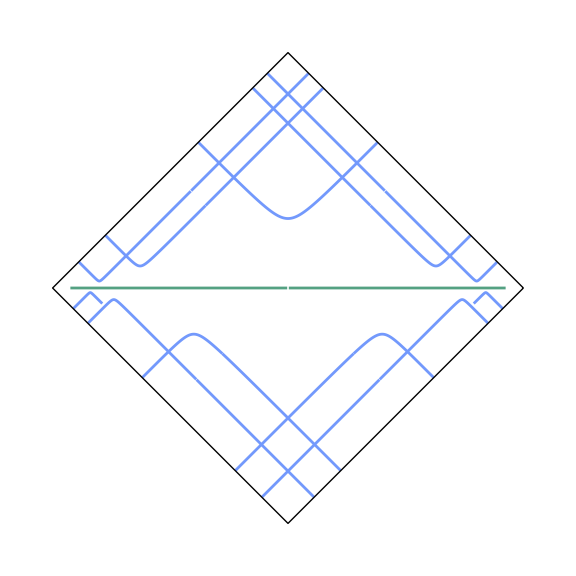

```mathematica
Module[{Penrose,PenroseBound,x,x1,x2,xH},
Penrose[v_]:={(ArcTan[v[[1]]+v[[2]]]+ArcTan[v[[1]]-v[[2]]])/2,(ArcTan[v[[1]]+v[[2]]]-ArcTan[v[[1]]-v[[2]]])/2};
PenroseBound=Graphics[{(*Dashed,*)Line[{{π/2,0},{0,π/2},{-π/2,0},{0,-π/2},{π/2,0}}]}];
x[t_]={t,0};
x1[ρ_][a_][b_][t_]=(t ρ (1-a^2 ρ^2+b^2 ρ^2)+ρ (2 a+t+a^2 t ρ^2-b^2 t ρ^2) Cosh[2 t ρ]-(1+a^2 ρ^2-b^2 ρ^2+2 a t ρ^2) Sinh[2 t ρ])/(2 ρ (Cosh[t ρ]^2+(a^2-b^2) ρ^2 Sinh[t ρ]^2-a ρ Sinh[2 t ρ]));
x2[ρ_][a_][b_][t_]=-b/(-Cosh[t ρ]^2+ρ (-((a^2-b^2) ρ Sinh[t ρ]^2)+a Sinh[2 t ρ]));
xH[ρ_][a_][b_][t_]={x1[ρ][a][b][t],x2[ρ][a][b][t]};
With[{
ρ=2ⅈ,
a=0,
b=0.5,
range=π/2,
l=2.1,
color1 = ColorData[95,"ColorList"][[2]],
color2 = ColorData[99,"ColorList"][[10]]
},
Show[{
ParametricPlot[Penrose@xH[ρ][a][b][t],{t,-2l,2l},
PlotRange->range,
PerformanceGoal->"Quality",
PlotStyle->blue,
ImageSize->Large,
PlotPoints->1000,
MaxRecursion->7
],
ParametricPlot[Penrose@x[t],{t,-4l,4l},PlotRange->range,PerformanceGoal->"Quality",PlotStyle->green,ImageSize->Large],
PenroseBound
},
Ticks->None,
Axes->None
]
]
]
```

```mathematica
Module[{Penrose,PenroseBound,x,x1,x2,xH},
Penrose[v_]:={(ArcTan[v[[1]]+v[[2]]]+ArcTan[v[[1]]-v[[2]]])/2,(ArcTan[v[[1]]+v[[2]]]-ArcTan[v[[1]]-v[[2]]])/2};
PenroseBound=Graphics[{(*Dashed,*)Line[{{π/2,0},{0,π/2},{-π/2,0},{0,-π/2},{π/2,0}}]}];
x[t_]={t,0};
x1[ρ_][a_][b_][t_]=(t ρ (1-a^2 ρ^2+b^2 ρ^2)+ρ (2 a+t+a^2 t ρ^2-b^2 t ρ^2) Cosh[2 t ρ]-(1+a^2 ρ^2-b^2 ρ^2+2 a t ρ^2) Sinh[2 t ρ])/(2 ρ (Cosh[t ρ]^2+(a^2-b^2) ρ^2 Sinh[t ρ]^2-a ρ Sinh[2 t ρ]));
x2[ρ_][a_][b_][t_]=-b/(-Cosh[t ρ]^2+ρ (-((a^2-b^2) ρ Sinh[t ρ]^2)+a Sinh[2 t ρ]));
xH[ρ_][a_][b_][t_]={x1[ρ][a][b][t],x2[ρ][a][b][t]};
With[{
ρ=2ⅈ,
a=0,
b=0.5,
range=π/2,
l=2.1,
color1 = ColorData[95,"ColorList"][[2]],
color2 = ColorData[99,"ColorList"][[10]]
},
Export["aspm.png",
Show[{
ParametricPlot[Penrose@xH[ρ][a][b][t],{t,-2l,2l},
PlotRange->range,
PerformanceGoal->"Quality",
PlotStyle->blue,
ImageSize->Large,
PlotPoints->1000,
MaxRecursion->7
],
ParametricPlot[Penrose@x[t],{t,-4l,4l},PlotRange->range,PerformanceGoal->"Quality",PlotStyle->green,ImageSize->Large],
PenroseBound
},
Ticks->None,
Axes->None
],
Background->None,
ImageResolution->144
]
]
];
```